```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\Dropbox\UFRJ\cursos\EEE457-Transmissão_Energia_Elétrica\arquivos_Mma_EEE457

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 16},ImageSize-> 600,Joined-> True,
PlotStyle-> {{Thick,Darker@Red},{Thick,Dashed,Darker@Blue},{Thick,DotDashed,Darker@Green},{Thick,Red,Dashed},{Thick,Green,Dashed},{Thick,Blue,Dashed}},
Axes-> False,Frame-> True];
```

```mathematica
SetOptions[{Plot,LogPlot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 16},ImageSize-> 600,
PlotStyle-> {{Thick,Darker@Red},{Thick,Dashed,Darker@Blue},{Thick,DotDashed,Darker@Green},{Thick,Red,Dashed},{Thick,Green,Dashed},{Thick,Blue,Dashed}},
Axes-> False,Frame-> True];
```

```mathematica
z1= I 0.267629;
y1= I 6.09755 10^-6;
Sb= 1500. 10^6;
Vb = 500.  10^3;
ib =Sb/(Sqrt[3] Vb);
Zb= Vb^2/Sb;
```

```mathematica
γ= Sqrt[z1 y1];
Zc= Sqrt[z1 /y1];
ℓ = 300.;
θ= γ ℓ;
```

```mathematica
a = Cosh[θ];
b = Zc Sinh[θ];
c = 1/Zc Sinh[θ];
Q={{a,b}, {c, a}};
```

```mathematica
Zb
```

166.667

```mathematica
MatrixForm[Q]
```

(0.92746+0. ⅈ | 0.+78.3378 ⅈ
0.+0.00178482 ⅈ | 0.92746+0. ⅈ)

```mathematica
{0.95, 1, 1.05}/a
```

{1.0243+0. ⅈ,1.07821+0. ⅈ,1.13212+0. ⅈ}

```mathematica
i1={Vb/Sqrt[3], ib};
o1=Q.i1;
```

```mathematica
Abs[o1[[1]]Sqrt[3]/Vb]
```

1.03976

```mathematica
Abs[o1[[2]]/ib]
```

0.973997

```mathematica
i2={0.95Vb/Sqrt[3], 1.05263 ib};
o2=Q.i2;
```

```mathematica
Abs[o2[[1]]Sqrt[3]/Vb]
```

1.0105

```mathematica
Abs[o2[[2]]/ib]
```

1.01635

```mathematica
i3={1.05Vb/Sqrt[3], 0.952381 ib};
o3=Q.i3;
```

```mathematica
Abs[o3[[1]]Sqrt[3]/Vb]
```

1.07179

```mathematica
Abs[o3[[2]]/ib]
```

0.936893

```mathematica
Arg[o3[[1]]Sqrt[3]/Vb]/π 180
```

24.687

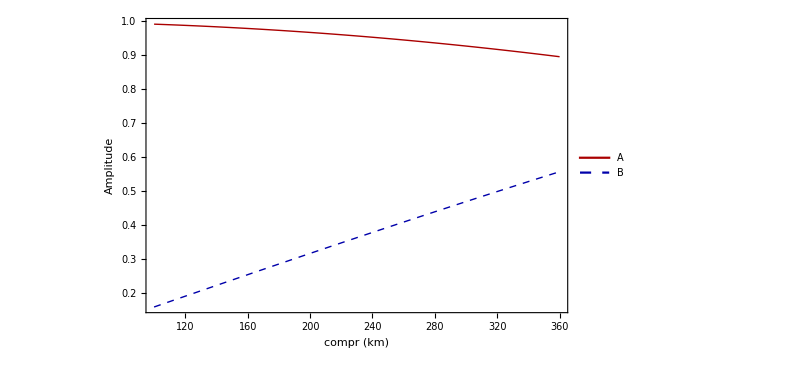

```mathematica
Plot[{Cosh[γ x], Im[Zc/Zb Sinh[γ x]]}, {x, 100, 360}, FrameLabel->{"compr (km)" ,"Amplitude"},PlotLegends->Placed[LineLegend[{"A","B"}],{.125,.75}]]
```